1/100 √(1/4+(9 π^2)/2)

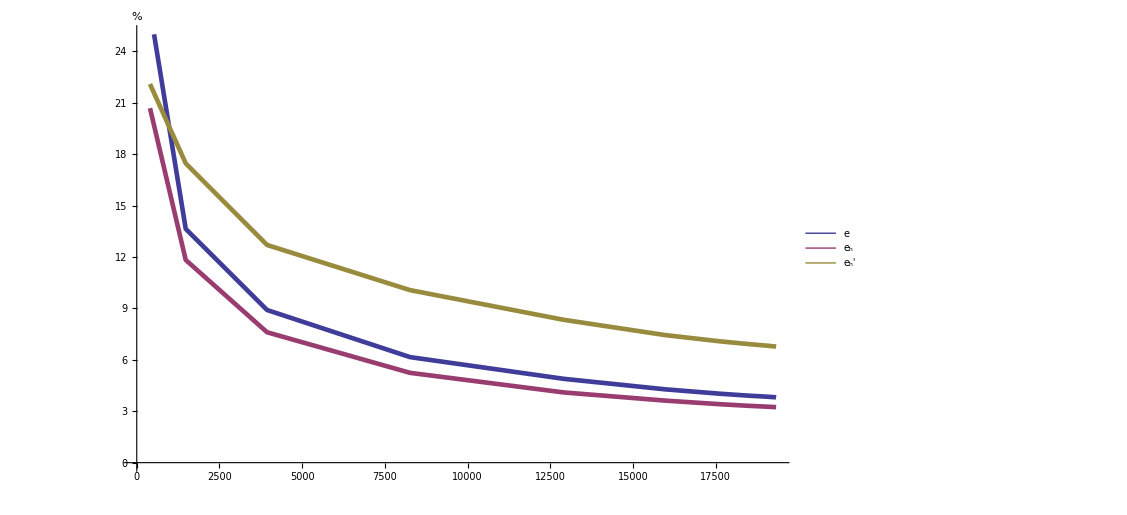

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem1\\my\\errors\\"];

u[x_,y_] = Sin[3*Pi*x]  Sin[3*Pi*y];
q[x_,y_] = u[x,y]^2+D[u[x,y],x]^2+D[u[x,y],y]^2;
norm = Sqrt[Integrate[q[x,y],{x,0,1},{y,0,1}]]/100
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];


ListLinePlot[{
	Transpose[{triangles, realErr/norm}],
	Transpose[{triangles, myErr/norm}],
	Transpose[{triangles, ostErr/norm}]
},
PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
PlotRange->{0,25},
BaseStyle->{FontSize->30},
PlotStyle->{Thickness->0.004,Thickness->0.004,Thickness->0.004},
AxesLabel->{"","%"}
]
```

```mathematica
,
```

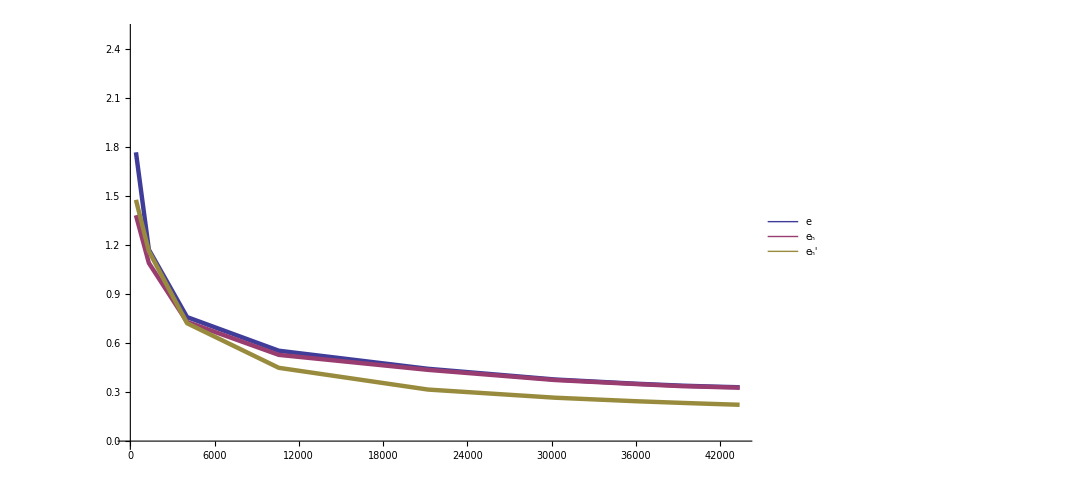

```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem1\\ost\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr/norm}],
	Transpose[{triangles, myErr/norm}],
	Transpose[{triangles, ostErr/norm}]
},
PlotLegends->Placed[{
ToExpression["e",TeXForm,HoldForm],
ToExpression["e_h",TeXForm,HoldForm],
ToExpression["e_h^\prime",TeXForm,HoldForm]
},{0.8,.5}],
BaseStyle->{FontSize->30},
PlotStyle->{Thickness->0.004,Thickness->0.004,Thickness->0.004},
PlotRange -> {0,25}]
```